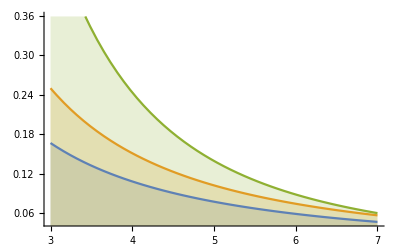

Piecewise[{{k^α x^(-1-α) α, x≥k}, {0, True}}]

Piecewise[{{1-(k/x)^α, x≥k}, {0, True}}]

```mathematica
Plot[Table[PDF[ParetoDistribution[3,α],x],{α,{.5,.75,1.5}}]//Evaluate,{x,3,3+4},Filling->Axis]
PDF[ParetoDistribution[k,α],x]
CDF[ParetoDistribution[k,α],x]
Manipulate[Plot[PDF[ParetoDistribution[k,α],x],{x,0,10}],{α,0.1,10},{k,0.1,10}]
```

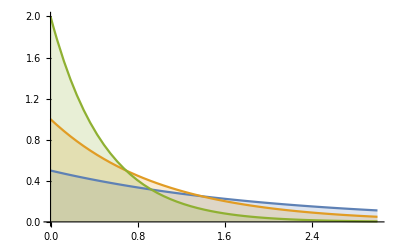

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

Piecewise[{{1-ⅇ^(-x λ), x≥0}, {0, True}}]

```mathematica
Plot[Table[PDF[ExponentialDistribution[λ],x],{λ,{1/2,1,2}}]//Evaluate,{x,0,3},Filling->Axis,PlotRange->All]
PDF[ExponentialDistribution[λ],x]
CDF[ExponentialDistribution[λ],x]
Manipulate[Plot[PDF[ExponentialDistribution[λ],x],{x,0,10}],{λ,0.1,10}]
```

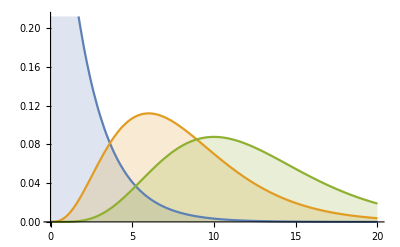

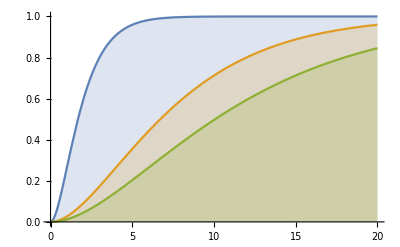

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

Piecewise[{{GammaRegularized[α,0,x/β], x>0}, {0, True}}]

```mathematica
Plot[Table[PDF[GammaDistribution[α,2],x],{α,{1,4,6}}]//Evaluate,{x,0,20},Filling->Axis]
Plot[Table[CDF[GammaDistribution[2,β],x],{β,{1,4,6}}]//Evaluate,{x,0,20},Filling->Axis]
PDF[GammaDistribution[α,β],x]
CDF[GammaDistribution[α,β],x]
Manipulate[Plot[PDF[GammaDistribution[α,β],x],{x,0,10}],{α,0.1,10},{β,0.1,10}]
```

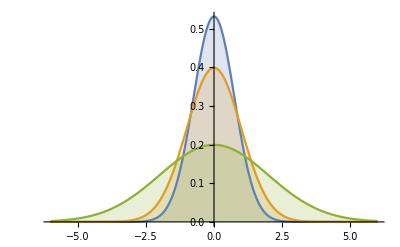

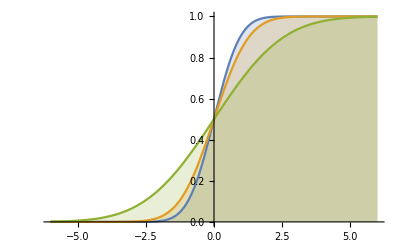

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
Plot[Table[CDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
PDF[NormalDistribution[μ,σ],x]
CDF[NormalDistribution[μ,σ],x]
Manipulate[Plot[PDF[NormalDistribution[μ,σ],x],{x,-10,10}],{μ,0,10},{σ,2,100}]
```

```mathematica
PDF[UniformDistribution[{a,b}],x]
CDF[UniformDistribution[{a,b}],x]
```

Piecewise[{{1/(-a+b), a≤x≤b}, {0, True}}]

Piecewise[{{(-a+x)/(-a+b), a≤x≤b}, {1, x>b}, {0, True}}]

```mathematica
Manipulate[Plot[PDF[NormalDistribution[μ,σ],x]/(1-CDF[NormalDistribution[μ,σ],x]),{x,-10,10}],{μ,-2,2},{σ,1,10}]
```

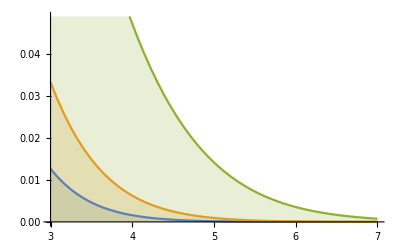

Piecewise[{{(ⅇ^-μ μ^k)/(k!), k≥0}, {0, True}}]

Piecewise[{{GammaRegularized[1+Floor[k],μ], k≥0}, {0, True}}]

```mathematica
Plot[Table[PDF[PoissonDistribution[μ],k],{μ,{.5,.75,1.5}}]//Evaluate,{k,3,3+4},Filling->Axis]
PDF[PoissonDistribution[μ],k]
CDF[PoissonDistribution[μ],k]
Manipulate[Plot[PDF[PoissonDistribution[μ],k],{k,0,100}],{μ,0.1,10}]
Manipulate[Plot[CDF[PoissonDistribution[μ],k],{k,0,10}],{μ,0.1,10}]
```

```mathematica
Plot[Table[PDF[PoissonProcess[μ][t],k],{μ,{.5,.75,1.5}}]//Evaluate,{k,3,3+4},Filling->Axis]
PDF[PoissonProcess[μ][t],k]
CDF[PoissonProcess[μ][t],k]
Manipulate[Plot[PDF[PoissonProcess[μ][t],k],{k,0,10}],{μ,0.1,10},{t,1,10}]
Manipulate[Plot[CDF[PoissonProcess[μ][t],k],{k,0,10}],{μ,0.1,10},{t,1,10}]
```

-Graphics-

Piecewise[{{(ⅇ^(-t μ) (t μ)^k)/(k!), k≥0}, {0, True}}]

Piecewise[{{GammaRegularized[1+Floor[k],t μ], k≥0}, {0, True}}]

```mathematica
Manipulate[Plot[{1/(k*D), ⅇ^(-k*D)},{D,1,10}],{k,0.0,1}]
```